```mathematica
(*Initiation: *)
```

```mathematica
v=9;
Do[
ichi[v][l]=Interpolation[Chi[v][l]];
,{l,{4,5,8,10,20,30,40,50,100,150,200}}]
```

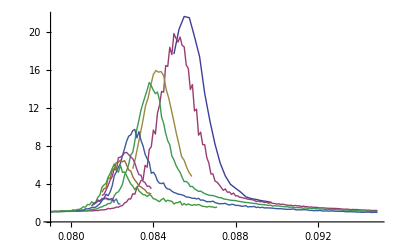

```mathematica
ListLinePlot[{Chi[v][4],Chi[v][5],Chi[v][8],Chi[v][10],Chi[v][20],Chi[v][30],Chi[v][40],Chi[v][50],Chi[v][150],Chi[v][200]},PlotRange->Full]
```

```mathematica
maxChi[v]=Table[{l*1000,Max[Chi[v][l][[All,2]]]},{l,{5,10,20,30,40,50}}]
LogmaxChi[v]=Table[{Log[maxChi[v][[All,1]][[i]]],Log[maxChi[v][[All,2]][[i]]]},{i,1,Length[maxChi[v]]}]

pmaxChi[v]=Table[{maxChi[v][[All,1]][[i]],Select[Chi[v][maxChi[v][[All,1]][[i]]/1000],#[[2]]==maxChi[v][[All,2]][[i]]&][[All,1]][[1]]},{i,1,Length[maxChi[v]]}]
```

```mathematica
maxChi[v]={{5000,19.85272},{10000,14.698399999999998},{20000,9.745742222222221},{30000,7.327303333333333},{40000,6.510505555555555},{50000,6.114174444444444}};
```

```mathematica
LogmaxChi[v]={{Log[5000],2.988341025453569},{Log[10000],2.687738644323388},{Log[20000],2.2768304944739617},{Log[30000],1.9916075537112783},{Log[40000],1.8734171115086926},{Log[50000],1.8106097550283204}};
```

```mathematica
maxChi[v]={{5000,0.085},{10000,0.0838},{20000,0.0831},{30000,0.0827},{40000,0.0824},{50000,0.0821}};
```

```mathematica
ν=1/0.09;
k0=0.08122;
ClearAll[a0,b0,d0,ex0,c0,x]
model1=a0*x-b0;
model2=d0+c0*x^(-ex0)
model3=d0+c0*x^(-1/ν)
model4=k0+c0*x^(-ex0)

nlf1=NonlinearModelFit[LogmaxChi[v],model,{a0,b0},x];

nlf1[{"BestFit","ParameterTable"}]


nlf2=NonlinearModelFit[pmaxChi[v],model2,{d0,c0,ex0},x];

nlf2[{"BestFit","ParameterTable"}]


nlf3=NonlinearModelFit[pmaxChi[v],model3,{d0,c0},x];

nlf3[{"BestFit","ParameterTable"}]


nlf4=NonlinearModelFit[pmaxChi[v],model4,{ex0,c0},x];

nlf4[{"BestFit","ParameterTable"}]
```

d0+c0 x^-ex0

d0+c0/x^0.09

0.08122+c0 x^-ex0

{7.60217-0.538855 x, | Estimate | Standard Error | t-Statistic | P-Value
a0 | 7.60217 | 0.225342 | 33.7362 | 4.60498×10^-6
b0 | 0.538855 | 0.0227035 | 23.7344 | 0.0000186859}

{0.0831833-470.944/x^59.1881, | Estimate | Standard Error | t-Statistic | P-Value
d0 | 0.0831833 | 0.000563143 | 147.713 | 6.84141×10^-7
c0 | -470.944 | 0. | -∞ | 0.
ex0 | 59.1881 | 0. | ∞ | 0.}

{0.0700307+0.0319543/x^0.09, | Estimate | Standard Error | t-Statistic | P-Value
d0 | 0.0700307 | 0.000637705 | 109.817 | 4.1232×10^-8
c0 | 0.0319543 | 0.00154511 | 20.681 | 0.0000322942}

{0.08122+0.434406/x^0.556265, | Estimate | Standard Error | t-Statistic | P-Value
ex0 | 0.556265 | 0.0283394 | 19.6286 | 0.0000397295
c0 | 0.434406 | 0.11294 | 3.84636 | 0.0183595}

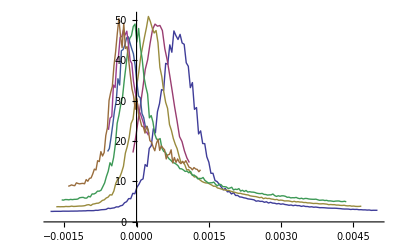

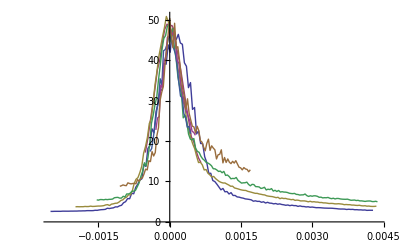

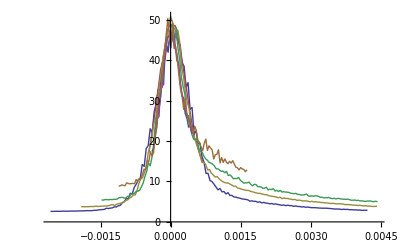

```mathematica
b0=-0.1;
k01=nlf2["ParameterTableEntries"][[1]][[1]];
k02=nlf3["ParameterTableEntries"][[1]][[1]];
k03=k0;
ex01=-nlf2["ParameterTableEntries"][[3]][[1]];
ex02=-1/ν;
ex03=-nlf4["ParameterTableEntries"][[1]][[1]];
a=-nlf1["ParameterTableEntries"][[2]][[1]];
c01=nlf2["ParameterTableEntries"][[2]][[1]];
c02=nlf3["ParameterTableEntries"][[2]][[1]];
c03=nlf4["ParameterTableEntries"][[2]][[1]];


Do[

(*absMs1[l]=Table[{(absM[l][[All,1]][[i]]),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];

absMs2[l]=Table[{(absM[l][[All,1]][[i]]-(k0+c0*l^(ex0))),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];

absMs[l]=Table[{(absM[l][[All,1]][[i]]-(k0+c0*l^(ex0)))*l^b,absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];*)

Chis1[v][l]=Table[{(Chi[v][l][[All,1]][[i]]-(k01+c01*(l*1000)^(ex01)))*(l*1000)^b0,Chi[v][l][[All,2]][[i]]*l^(-a)},{i,1,Length[Chi[v][l]]}];

Chis2[v][l]=Table[{(Chi[v][l][[All,1]][[i]]-(k02+c02*(l*1000)^(ex02)))*(l*1000)^b0,Chi[v][l][[All,2]][[i]]*l^(-a)},{i,1,Length[Chi[v][l]]}];

Chis3[v][l]=Table[{(Chi[v][l][[All,1]][[i]]-(k03+c03*(l*1000)^(ex03)))*(l*1000)^b0,Chi[v][l][[All,2]][[i]]*l^(-a)},{i,1,Length[Chi[v][l]]}];

,{l,{5,8,10,20,30,40,50,150,200}}]
(*ListLogPlot[{absM[16],absM[24],absM[32],absM[48],absM[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{absMs1[16],absMs1[24],absMs1[32],absMs1[48],absMs1[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{absMs2[16],absMs2[24],absMs2[32],absMs2[48],absMs2[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{absMs[16],absMs[24],absMs[32],absMs[48],absMs[64]},Joined->True,PlotMarkers->Automatic]*)
ListPlot[{Chis1[v][5],Chis1[v][8],Chis1[v][10],Chis1[v][20],Chis1[v][30],Chis1[v][40],Chis1[v][50]},Joined->True]
ListPlot[{Chis2[v][5],Chis2[v][8],Chis2[v][10],Chis2[v][20],Chis2[v][30],Chis2[v][40],Chis2[v][50]},Joined->True]
ListPlot[{Chis3[v][5],Chis3[v][8],Chis3[v][10],Chis3[v][20],Chis3[v][30],Chis3[v][40],Chis3[v][50]},Joined->True]
```

```mathematica
l1=10;
l2=50;

Do[
(*input1[l]=Table[{(absM[l][[All,1]][[i]]-(k01+c01*l^(ex01))),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];

input2[l]=Table[{(absM[l][[All,1]][[i]]-(k02+c02*l^(ex02))),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];*)

input3[l]=Table[{(Chi[v][l][[All,1]][[i]]-(k03+c03*(l*1000)^(ex03))),Chi[v][l][[All,2]][[i]]*l^(-a)},{i,1,Length[Chi[v][l]]}];
,{l,{l1,l2}}]

aux=1000;
For[z=-0.2,z<0.4,z+=0.1,
ClearAll[i];

Do[
dat[l]=Table[{input3[l][[All,1]][[i]]*(l*1000)^z,input3[l][[All,2]][[i]]},{i,1,Length[input3[l]]}];
i[l]=Interpolation[dat[l]]
,{l,{l1,l2}}];


min=Max[dat[l1][[All,1]][[1]],dat[l2][[All,1]][[1]]];
max=Min[dat[l1][[All,1]][[Length[dat[l1]]]],dat[l2][[All,1]][[Length[dat[l2]]]]];

val=NIntegrate[Abs[i[l1][x]-i[l2][x]],{x,min,max}]/(max-min);
Print[val]

If[val<aux,
aux=val;
zf=z;
]
]

aux
"= zf"zf
```

4.20093

3.97295

4.47643

5.64189

6.99752

8.44489

3.97295

-0.1 = zf

```mathematica
l1=5;
l2=10;
l3=30;
l4=50;

Do[
(*input1[l]=Table[{(absM[l][[All,1]][[i]]-(k01+c01*l^(ex01))),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];

input2[l]=Table[{(absM[l][[All,1]][[i]]-(k02+c02*l^(ex02))),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];*)

input3[l]=Table[{(Chi[v][l][[All,1]][[i]]-(k03+c03*(l*1000)^(ex03))),Chi[v][l][[All,2]][[i]]*l^(-a)},{i,1,Length[Chi[v][l]]}];
,{l,{l1,l2,l3,l4}}]

sum={};

aux=1000;
For[z=-0.4,z<0.4,z+=0.01,
ClearAll[i];

Do[
dat[l]=Table[{input3[l][[All,1]][[i]]*(l*1000)^z,input3[l][[All,2]][[i]]},{i,1,Length[input3[l]]}];
i[l]=Interpolation[dat[l]]
,{l,{l1,l2,l3,l4}}];


min=Max[dat[l1][[All,1]][[1]],dat[l2][[All,1]][[1]],dat[l3][[All,1]][[1]],dat[l4][[All,1]][[1]]];
max=Min[dat[l1][[All,1]][[Length[dat[l1]]]],dat[l2][[All,1]][[Length[dat[l2]]]],dat[l3][[All,1]][[Length[dat[l3]]]],dat[l4][[All,1]][[Length[dat[l4]]]]];

val=NIntegrate[Abs[Max[i[l1][x],i[l2][x],i[l3][x],i[l4][x]]-Min[i[l1][x],i[l2][x],i[l3][x],i[l4][x]]],{x,min,max}]/(max-min);
(*Print[val];*)

sum=Append[sum,{z,val}];

If[val<aux,
aux=val;
zf=z;
]
]

aux
"= zf"zf
```

9.16026

0.12 = zf

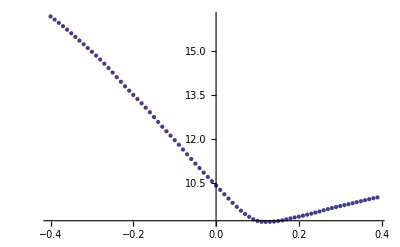

```mathematica
ListPlot[sum]
```